```mathematica
(* Find Root *)
FindRoot[Sin[x]==0,{x,6.}]
```

{x→6.28319}

```mathematica
FindRoot[x^2-1==0,{x,0}]
```

FindRoot::jsing: Encountered a singular Jacobian at the point {x} = {0.}. Try perturbing the initial point(s). More…

{x→0.}

```mathematica
FindRoot[x^2-1==0,{x,RandomReal[]}]
```

{x→1.}

```mathematica
FindRoot[Zeta[0.5-t]==0,{t,{12,13}}]
```

{t→{12.5,12.5}}

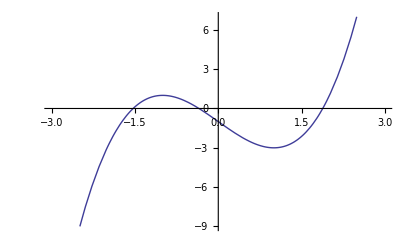

```mathematica
f[x_]=x^3-3 x-1;
Plot[f[x],{x,-3,3}]
```

```mathematica
FindRoot[f[x]==0,{x,1.5}]
FindRoot[f[x]==0,{x,0}]
FindRoot[f[x]==0,{x,0.76}]
```

{x→1.87939}

{x→-0.347296}

{x→-1.53209}

```mathematica
FindRoot[x Sin[x]-1==0,{x,18,21}]
```

{x→18.9025}

```mathematica
FindRoot[{x^2+y^2-1==0,x^3-y==0},{x,0.8},{y,0.6}]
```

{x→0.826031,y→0.563624}